15-x

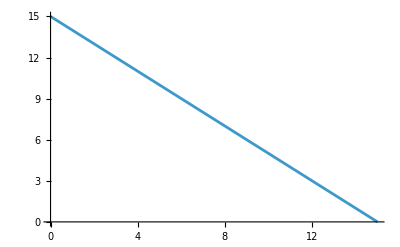

225/2

2/225

(2 (15-x))/225

```mathematica
g=15-x
Plot[g,{x,0,15}]
A=Integrate[g,{x,0,15}]
k=1/A
f=k g
```

```mathematica
EV=Integrate[x f,{x,0,15}]
Var=Integrate[(x-EV)^2 f,{x,0,15}]
```

5

25/2

```mathematica
F=Integrate[f,{x,0,x}]
```

(2 x)/15-x^2/225

```mathematica
D[F,x]
f//Expand
```

2/15-(2 x)/225

2/15-(2 x)/225

```mathematica
Integrate[f,{x,0,5.51317}]//N
```

0.6

```mathematica
Solve[F==.6,x]
```

{{x→5.51317},{x→24.4868}}

To find a percentile p, we just need to set F = p and solve.

```mathematica
F=Integrate[f,{x,0,x}]
p=0.6
Solve[F==p,x]
```

(2 x)/15-x^2/225

0.95

{{x→11.6459},{x→18.3541}}

```mathematica
p=0.95
Solve[F==p,x]
```

0.95

{{x→11.6459},{x→18.3541}}

```mathematica
Integrate[f,{x,10,15}]
```

1/9

```mathematica
Integrate[f,{x,0,3}]
```

9/25

```mathematica
$Assumptions=σ>0;
f=1/Sqrt[2*π*σ^2] Exp[-1/2*((x-μ)/σ)^2];
bounds={x,-Infinity,Infinity};
EV=Integrate[x f,bounds]
Var=Integrate[(x-EV)^2 f,bounds]
$Assumptions=Null
```

μ

σ^2

```mathematica
σ=5;
μ=21;
f=1/Sqrt[2*π*σ^2] Exp[-1/2*((x-μ)/σ)^2];
F=Integrate[f,{x,0,x}];
p=.9;
Solve[F==p,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→27.4081}}

```mathematica
p=.99
Solve[F==p,x]
```

0.99

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→32.6342}}